# PS 15 — Rania 4.1.2025

## 37

```mathematica
(*37.1 Make a list of numbers up to 100,with even numbers on yellow and odd numbers on light gray.*)
If[EvenQ[#]==True , Style[#, Background->Yellow], Style[#, Background -> LightGray]]&/@ Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(*37.2 Make a list of numbers up to 100, with primes framed*)
```

```mathematica
If[PrimeQ[#]==True, Framed[#], #]&/@ Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(*37.3 Make a list of numbers up to 100,with primes framed and labeled in light gray with their values modulo 4.*)

If[PrimeQ[#]==True, Labeled[Framed[#], Style[Mod[#,4], LightGray]], #]&/@Range[100]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

```mathematica
(*37.4 Create a 3×6 GraphicsGrid of randomly colored disks.*)
```

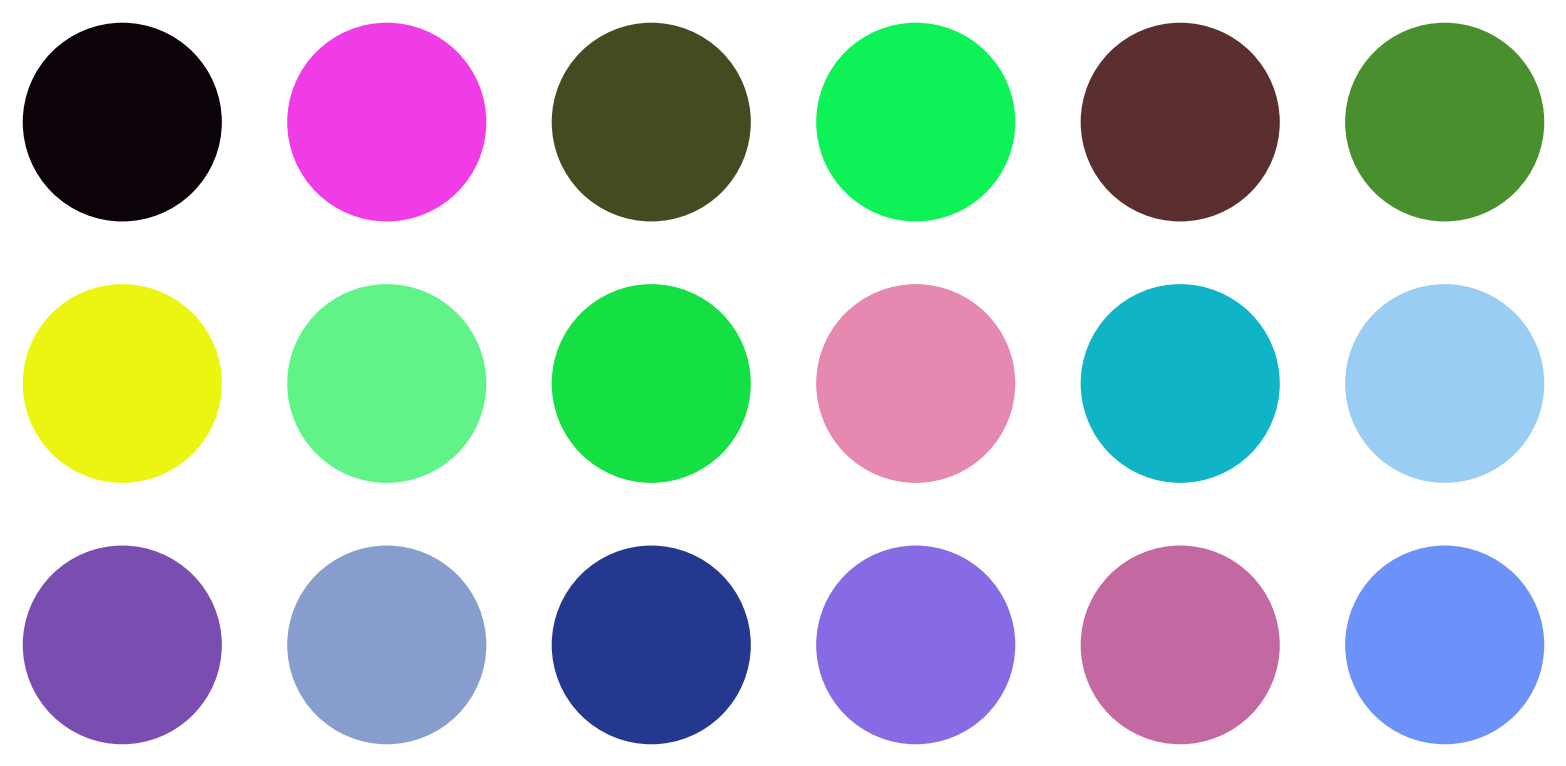

```mathematica
Table[Graphics[Style[Disk[],RandomColor[]]],3,6]//GraphicsGrid
(*what's the third argument style of Table again?*)
```

```mathematica
(*37.5 Make a pie chart of the GDPs of the countries in the G5,labeling each wedge.*)

PieChart[EntityList[EntityClass["Country","GroupOf5"]["GDP"]], ChartLabels -> EntityClass["Country","GroupOf5"]["Name"]]
(*technique of ["Name"]*)
```

-Graphics-

```mathematica
(*37.6 Make a pie chart of the populations of the countries in the G5,giving a legend for each wedge.*)
PieChart[EntityList[["GDP"]], ChartLegends-> ["Name"]]
```

-Graphics-

```mathematica
(*37.7 Make a 5×5 GraphicsGrid of pie charts that give the relative frequencies of digits in 2^n with n starting at 1.*)
Partition[Table[PieChart[Counts[IntegerDigits[2^n]]],{n,25}],5]//GraphicsGrid
```

-Graphics-

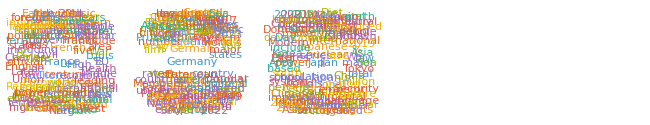

```mathematica
(* 37.8 Make a graphics row of word clouds for Wikipedia articles on the G5 countries.*)
WordCloud[WikipediaData[#]]&/@EntityList[EntityClass["Country","GroupOf5"]]//GraphicsRow
```

## 38 - variables!

```mathematica
(*38.1 Use Module to compute x^2+x where x is Range[10]*)
Module[{x= Range[10]}, x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
(*38.2 Use Module to generate a list of 10 random integers up to 100,then make a column giving the original list,and the results of applying Sort,
Max and Total to it*)
Module[{randomint = RandomInteger[100,10]},Column[{randomint, Sort[randomint], Max[randomint ], Total[randomint]}]]
```

{8,49,61,36,82,98,11,32,71,92}
{8,11,32,36,49,61,71,82,92,98}
98
540

```mathematica
(*38.3 Use Module to generate an image collage from a picture of a giraffe,and the results of applying Blur,EdgeDetect and ColorNegate to it.*)
Module[{x=Entity["TaxonomicSpecies","GiraffaCamelopardalis::y5488"][EntityProperty["TaxonomicSpecies","Image"]]},ImageCollage[{x,Blur[x], EdgeDetect[x], ColorNegate[x]}]]
```

-Graphics-

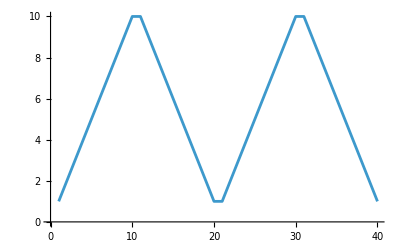

```mathematica
(*38.4 Inside a Module,let r=Range[10],then make a line plot of r joined with the reverse of r joined with r joined with the reverse of r.*)
Module[{r= Range[10]}, ListLinePlot[Join[r, Reverse[r],r,Reverse[r]]]]
```

```mathematica
(*38.5 Find a simpler form for {Range[10]+1,Range[10]-1,Reverse[Range[10]]}.*)
{Range[10]+1, Range[10]-1, Reverse[Range[10]]}
Module[{x=Range[10]}, {x+1,x-1, Reverse[x]}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
(*38.6 Find a simpler form for Module[{u=10},Join[{u},Table[u=Mod[17u+2,11],20]]].*)
Module[{u=10}, Join[{u}, Table[u=Mod[17u+2,11],20]]]
NestList[Mod[17#+2, 11]&, 10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
(*38.7 Generate 10 random strings made of 5 letters,in which consonants (non-vowels) alternate with vowels (aeiou).*)
vowels={"a", "e", "i", "o", "u", "y"};
constants = Complement[Alphabet[],vowels];

Table[StringJoin[RandomSample[constants,1], RandomSample[vowels,1], RandomSample[constants,1], RandomSample[vowels,1], RandomSample[constants,1]],5]
```

{sakin,pebyg,parux,fizyc,ludyp}